```mathematica
<<Toolbox`
<<Toolbox`Style`
```

# Notation

## Metabolites

Metabolites are defined in the following way:

```mathematica
metabolite["atp","c"]
```

atp^c

or using the following shorthand form

```mathematica
m["atp","c"]
```

atp^c

Metabolite atp^c represents the compound ‘atp’ in compartment ‘c’.

```mathematica
metabolite["atp",_]
```

atp^_

represents the compound ‘atp’ in any compartment (using the underscore pattern _).

Furthermore, external metabolites, whose concentrations are assumed to be constant (e.g. in sink or source reactions),  can be specified in the following way:

```mathematica
metabolite["atp","Xt"]
```

atp^Xt

Compartment specifications are optional and can be omitted if no explicit modeling of compartments is necessary:

```mathematica
metabolite["atp"]
```

atp

Furthermore, metabolites can be defined using the function str2mass and the following convention: “metaboliteID_compartment” (or “metaboliteID[compartment]”).

```mathematica
str2mass["atp_c"]
str2mass["atp[c]"]
str2mass["atp_any"]
```

atp^c

atp^c

atp^any

It is very important to make clear that although metabolites (and many of the following data types) are displayed in a human readable format (e.g atp^c), the internal representation is still exactly in the metabolite[id, compartment] form,

```mathematica
FullForm[atp^c]
```

metabolite["atp","c"]

and in this respect very similar to other Mathematica definitions, e.g.,

```mathematica
FullForm[∑_(n=0)^m 1/f[n]]
```

Sum[Power[f[n],-1],List[n,0,m]]

It is possible to use “Menu → Evaluation → Evaluate in place“ in the menu (or Cmd + Shift + Enter or the mouse context menu) for inplace replacements

Select the next line and evaluate it ‘in-place’

```mathematica
metabolite["atp", "c"]
```

You can get back to InputForm by using the mouse context menu or by pressing Cmd + Shift + I (same as Menu → Cell → Convert to → InputForm)

Select the following metabolite and convert it back to InputForm

```mathematica
atp^c
```

## Reactions

Reactions are defined in the following way (using reaction)

```mathematica
reaction["vpfk",{m["atp","c"],m["f6p","c"]},{m["adp","c"],m["fbp","c"],m["h","c"]},{1,1,1,1,1}]
```

(atp^c+f6p^c⇌adp^c+fbp^c+h^c)^vpfk

or in shorthand form (using r)

```mathematica
r["vpfk",{m["atp","c"],m["f6p","c"]},{m["adp","c"],m["fbp","c"],m["h","c"]},{1,1,1,1,1}]
```

(atp^c+f6p^c⇌adp^c+fbp^c+h^c)^vpfk

The first position in the arguments list is the reactions’s ID, second and third represent substrates and products, respectively, and the fourth provides the stoichiometric factors. Reactions are assumed to be reversible per default. A boolean, fifth argument has to be provided if one wants to define an irreversible reaction (True=reversible, False=irreversible).

```mathematica
r["vpfk",{m["atp","c"],m["f6p","c"]},{m["adp","c"],m["fbp","c"],m["h","c"]},{1,1,1,1,1},False]
```

(atp^c+f6p^c→adp^c+fbp^c+h^c)^vpfk

Furthermore, reactions can be defined using string definitions by using the following convention: “reactionID: met_compartment (--> or <=>) met2_compartment + 
met3_compartment ”.

```mathematica
str2mass["vpfk: atp_c + f6p_c <=> adp_c + fbp_c + h_periplasm"]
str2mass["vpfk: atp[c] + f6p[c] <=> adp[c] + fbp[c] + h[periplasm]"]
str2mass["vpfk: atp_c + f6p_c --> adp_c + fbp_c + h_c"]
```

(atp^c+f6p^c⇌adp^c+fbp^c+h^periplasm)^vpfk

(atp^c+f6p^c⇌adp^c+fbp^c+h^periplasm)^vpfk

(atp^c+f6p^c→adp^c+fbp^c+h^c)^vpfk

Exchange reactions or sinks can be specified by either leaving the substrates or products list empty, e.g.,

```mathematica
r["EX_atp",{m["atp","c"]},{},{1},True]
```

(atp^c⇌∅)^EX_atp

or by indicating a sink with “0”, e.g.,

```mathematica
str2mass["EX_atp: atp[c] <=> 0"]
```

(atp^c⇌∅)^EX_atp

Write out the following reaction: L-Malate + NAD → Oxaloacetate + NADH

```mathematica
(*Put your code here*)
```

## Fluxes

A flux of a reaction is specified using the v expression.

```mathematica
v["vtpi"]
```

v_vtpi

## Parameters

#### Equilibrium constants

```mathematica
Keq["vtpi"]
```

K_vtpi

```mathematica
str2mass["Keq_vtpi"]
```

K_vtpi

#### Rate constants

```mathematica
rateconst["vtpi",True]
```

k_vtpi^⟶

```mathematica
rateconst["vtpi", True]
```

k_vtpi^⟶

```mathematica
rateconst["vtpi",False]
```

k_vtpi^⟵

#### Fixed external concentrations

```mathematica
metabolite["atp","Xt"]
```

atp^Xt

#### Arbitrary parameters

```mathematica
parameter["Param"]
```

Param_Global

```mathematica
parameter["Param","vtpi"]
```

Param_vtpi

```mathematica
FullForm[Underscript[Param, vtpi]]
```

parameter["Param","vtpi"]

## Type related functions

Keq, metabolite, reaction, rateconst, etc. implement a series of functions, e.g., getID, getCompartment, reversibleQ etc.,

```mathematica
getID[Underscript[K, vtpi]]
getID[(atp^c⇌∅)^EX_atp]
getID[atp^Xt]
```

vtpi

EX_atp

atp

```mathematica
reversibleQ[(atp^c⇌∅)^EX_atp]
getCompartment[(atp^c⇌∅)^EX_atp]
getCompartment[Overscript[atp^compartment1⇌atp^compartment2, Translocation]]
```

True

c

{compartment1,compartment2}

## String representations

ToString has been overloaded with respect to the data types, e.g.

```mathematica
ToString[Underscript[K, vtpi]]
```

Keq_vtpi

```mathematica
ToString[Overscript[atp^compartment1⇌atp^compartment2, Translocation]]
```

Translocation: atp[compartment1] <=> atp[compartment2]

## More data types ...

### Enzymes

```mathematica
enz=enzyme["ID"->"PFK","Compartment"->"c"]
```

(PFK^c)_^

```mathematica
bindActivator[enz,m["atp","c"]]
bindInhibitor[enz,m["atp","c"]]
bindCatalytic[enz,m["atp","c"]]
```

(PFK^c)_^(atp^c)

(PFK^c)_(atp^c)^

(PFK^c&atp^c)_^

See ???.nb for a detailed introduction into enzymes and regulatory modules

### Genes, proteins and complexes

```mathematica
gene["b3916"]
```

b3916

```mathematica
protein["PfkA"]
```

PfkA

```mathematica
geneComplex[gene["b0902"],gene["b0903"]]
```

b0902 | b0903

```mathematica
proteinComplex[protein["PflBec"],protein["YfiD"]]
```

PflBec | YfiD

```mathematica
gpr={{{PflBec, YfiD}}->"PFL",PflBec->"PFL",TdcEec->"PFL",PflDec->"PFL",{{b0902, b0903}}->PflBec,{{b3951, b3952}}->PflDec,{{b0902, b3114}}->TdcEec,{{b0902, b0903}}->{{PflBec, YfiD}},b2579->{{PflBec, YfiD}}};
```

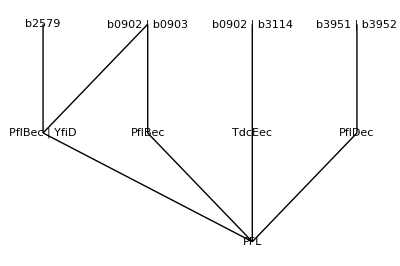

```mathematica
visualizeGPR[gpr]
```

### Complex

```mathematica
cmplx=complex[m["Mg+"],m["ATP"]]
```

Mg+ | ATP

```mathematica
getID[cmplx]
```

Mg+ & ATP